## Load package

```mathematica
SetDirectory[NotebookDirectory[]];
<<"ExtFileLoading.wl";
<<"DegFileNamings.wl";
<<"ArrayManip.wl";
<<"PlotMatexFormatting.wl";
SetDirectory[NotebookDirectory[]<>"/.."];
```

## Functions

```mathematica
dataLogsErrsFun[xLst_,yLst_,yVarLst_]:=Module[{dataLst,dataLogLst,dataAroundLst,dataLogAroundLst,xLogLst,yLogLst,yAroundLst,yLogVarLst,yLogAroundLst,logFitMod},
dataLst={xLst,yLst}ᵀ;
xLogLst=Log[xLst];
yLogLst=Log[yLst];
dataLogLst={xLogLst,yLogLst}ᵀ;
yAroundLst=makeDataErr[yLst,yVarLst];
dataAroundLst={xLst,yAroundLst}ᵀ;
yLogVarLst=yVarLst/yLst;
yLogAroundLst=makeDataErr[yLogLst,yLogVarLst];
dataLogAroundLst={xLogLst,yLogAroundLst}ᵀ;
logFitMod=LinearModelFit[dataLogLst,{x},{x},Weights->1/yLogVarLst^2,VarianceEstimatorFunction->(1&)];
{logFitMod,yLogVarLst,dataLst,dataLogLst,dataAroundLst,dataLogAroundLst}
];
```

## Plot <N> scaling

### Define parameters

```mathematica
nDim=3;
divLstBase={80,64,64};
nLst=Table[n,{n,10,60,5}];
nLen=Length[nLst];
itNum=100;
seed=1000;
```

```mathematica
nBase=10;
```

```mathematica
levLowLst
```

{4,6,8,10,12,14,16,18,20,22,24}

```mathematica
nRat=0.4;
levLowLst=Floor[nRat nLst];
levHighLst=Ceiling[nRat nLst];
```

```mathematica
k3LowRat=0.3;
k3HighRat=1-k3LowRat;
```

```mathematica
fMain="deg";
fModMethod="flux";
```

### Plotting options

```mathematica
figW=5cm;
pres=3;
presErr=1;
capLoc={0.9,0.15};
```

```mathematica
dataLab=MaTeX[#,Magnification->1]&/@{"\\mathrm{data}"};
```

### storage arrays

```mathematica
gLstFull=Table[ConstantArray[0,{itNum,nLst⟦nId⟧}],{nId,1,nLen}];
```

```mathematica
delCLst=Table[ConstantArray[0,{nLst⟦nId⟧-1,Floor[80 √(nLst⟦nId⟧/nBase)]}],{nId,1,nLen}];
delCVarLst=Table[ConstantArray[0,{nLst⟦nId⟧-1,Floor[80 √(nLst⟦nId⟧/nBase)]}],{nId,1,nLen}];
```

### Loading files

```mathematica
For[nId=1,nId<=nLen,nId++,
mSz=nLst⟦nId⟧;
divLst=Floor[√(mSz/nBase)divLstBase];
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fNameN=fNameFun[fMain,attrLstDim,valLstDim,fModMethod,jld2Type];
gLstPolN=readJuliaVarSqDim[fNameN,"NLstPol"];
gLstFull⟦nId⟧=gLstPolN⟦1⟧;
fNameC=fNameFun["deltaN_distill",attrLst,valLst,fModMethod,jld2Type];
delCtmp=readJuliaVarDimFixed[fNameC,"deltaNsq"];
delCLst⟦nId⟧=delCtmp;
fNameCVar=fNameFun["deltaVar_distill",attrLst,valLst,fModMethod,jld2Type];
delCVarTmp=readJuliaVarDimFixed[fNameCVar,"deltaNvar"];
delCVarLst⟦nId⟧=delCVarTmp;]
```

```mathematica
fNameC=fNameFun["deltaN_distill",attrLst,valLst,fModMethod,jld2Type];
```

```mathematica
fNameC
```

deltaN_distill_N_60_param_divide_[195, 156, 156]_instanceNum_100_seed_1000_flux.jld2

```mathematica
delCtmp=readJuliaVarSq[fNameC,"deltaNsq"];
```

```mathematica
delCVarTmp=readJuliaVar[fNameCVar,"deltaNvar"];
```

```mathematica
delCVarTmp//Dimensions
```

{59,195}

```mathematica
gLstPolN//Dimensions
```

{2,60,100}

```mathematica
gLstFull⟦-1⟧//Dimensions
```

{60,100}

```mathematica
delCtmp//Dimensions
```

{59,195}

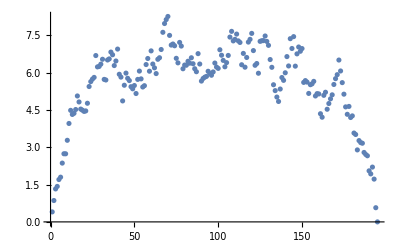

```mathematica
ListPlot[delCVarTmp⟦1⟧]
```

```mathematica
xyLabsC=MaTeX[#,Magnification->labMag]&/@{"k_3 / 2\\pi","\\langle S_n \\rangle"};
```

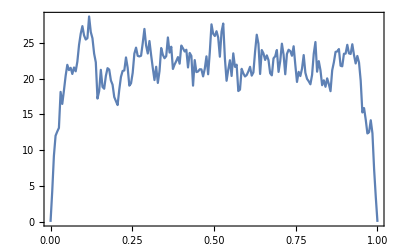

```mathematica
Show[ListLinePlot[{Table[z,{z,0,1,1/Length[delCtmp⟦24⟧]}],{delCtmp⟦24,-1⟧}~Join~delCtmp⟦24⟧}ᵀ],ImageSize->{Automatic,figW},BaseStyle->texStyle,Frame->True,PlotRangePadding->None,FrameLabel->xyLabsC]
```

### Plotting

```mathematica
Map[f,{{1,2},{3,4}},{2}]
```

{{f[1],f[2]},{f[3],f[4]}}

```mathematica
gLstTotal=Total/@gLstFull;
gLstTotalMean=Mean/@gLstTotal//N;
gLstTotalStd=StandardDeviation/@gLstTotal//N;
```

```mathematica
gLstLevelsMean=Map[Mean,gLstFull,{2}]//N;
gLstLevelsStd=Map[StandardDeviation,gLstFull,{2}]//N;
```

```mathematica
gLstLevelsStd//Dimensions
```

{11}

```mathematica
gLstRatLevMean//Dimensions
```

{11}

```mathematica
gLstTotalMean//Dimensions
```

{11}

```mathematica
gLstLevelsMean//Dimensions
```

{11}

```mathematica
gLstLevelsMean⟦1⟧
```

{11.52,32.06,48.28,58.68,62.73,62.73,58.68,48.28,32.06,11.52}

```mathematica
gLstTotalMean
```

{426.54,1183.13,2431.36,4213.92,6583.38,9648.18,13362.5,17859.6,23154.6,29285.3,36251.6}

```mathematica
gLstFull//Dimensions
```

{11}

```mathematica
gLstLevelsMean⟦2⟧//Dimensions
```

{100}

```mathematica
gLstFull⟦1⟧//Dimensions
```

{10,100}

```mathematica
gLstFull⟦7⟧//Dimensions
```

{40,2}

```mathematica
gLstLevelsMean
```

{{38.8,38.8},{76.1333,76.1333},{125.9,125.9},{179.88,179.88},{227.6,227.6},{277.771,277.771},{336.25,336.25},{391.289,391.289},{472.86,472.84},{521.073,521.073},{618.983,618.983}}

```mathematica
levLowLst⟦4⟧
```

10

```mathematica
gLstRatLevMean
```

```mathematica
gLstRatLevStd
```

{5.9099,8.91157,11.1608,13.9629,16.2295,16.3195,21.3029,23.7654,23.7688,29.0773,23.9099}

```mathematica
gLstRatLevMean//Dimensions
```

{11}

```mathematica
gLstRatLevMean=Table[gLstLevelsMean⟦nId,levLowLst⟦nId⟧⟧,{nId,1,nLen}];
gLstRatLevStd=Table[gLstLevelsStd⟦nId,levLowLst⟦nId⟧⟧,{nId,1,nLen}];
```

```mathematica
fitLevRat["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.692148 | 0.127831 | 5.41458 | 0.000424834
n | 1.47895 | 0.0341084 | 43.3603 | 9.21622×10^-12

```mathematica
{fitLevRat,gLstRatLevLogVar,gLstRatLevData,gLstRatLevDataLog,gLstRatLevDataAround,gLstRatLevDataLogAround}=dataLogsErrsFun[nLst,gLstRatLevMean,gLstRatLevStd];
```

```mathematica
{fitTotal,gLstTotalLogVar,gLstTotalData,gLstTotalDataLog,gLstTotalDataAround,gLstTotalDataLogAround}=dataLogsErrsFun[nLst,gLstTotalMean,gLstTotalStd];
```

```mathematica
expLevRat=fitLevRat["ParameterTableEntries"]⟦2,1⟧;
```

```mathematica
expLevRatStd=fitLevRat["ParameterTableEntries"]⟦2,2⟧;
```

```mathematica
{expTotal,expTotalStd}=fitTotal["ParameterTableEntries"]⟦2,1;;2⟧;
```

```mathematica
{expTotal,expTotalStd}
```

{2.46507,0.0201367}

```mathematica
Log[512/(135 √(3π))]//N
```

0.211379

```mathematica
fitOnlyC=NonlinearModelFit[gLstTotalDataLog,2.5ln+c,{c},ln];
```

```mathematica
fitOnlyC["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c | 0.28516 | 0.0048506 | 58.7887 | 4.92505×10^-14

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {1, 0.3720017578386305, 0.01426313000936944, 26.081355045790282, 8.640622920627265*^-10}, {n, 2.4746556319434885, 0.004111117335288358, 601.9423504899584, 4.9071869470200895*^-22}}
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.372002 | 0.0142631 | 26.0814 | 8.64062×10^-10
n | 2.47466 | 0.00411112 | 601.942 | 4.90719×10^-22

```mathematica
xyLabs=MaTeX[#,Magnification->labMag]&/@{"M","\\frac{\\langle N^{\\pm} \\rangle}{\\langle N^{\\pm} \\rangle_{\\rm WW}}"};
```

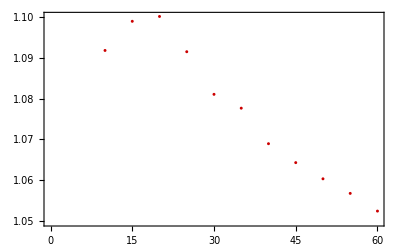

```mathematica
pltWWEcmp2=ListPlot[{nLst,gLstTotalMean/(512/(135 √(3π))nLst^(5/2))}ᵀ,Frame->True,ImageSize->{Automatic,5cm},PlotRangePadding->{{None,Automatic},Automatic},BaseStyle->texStyle,FrameLabel->xyLabs,PlotStyle->darkRed,PlotMarkers->{Automatic,AbsolutePointSize[3]}]
```

```mathematica
Directory[]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules

```mathematica
Export["figs\\pltWWEcmp.pdf",pltWWEcmp2]
```

figs\pltWWEcmp.pdf

```mathematica
"figs\\pltWWEcmp.pdf"
```

figs\pltWWEcmp.pdf

```mathematica
expLevRatStd
```

0.0341084

```mathematica
xyLabsTotal=MaTeX[#,Magnification->labMag]&/@{"M","\\log \\langle N^{\\pm} \\rangle"}
```

{-Graphics-,-Graphics-}

```mathematica
xyLabs=MaTeX[#,Magnification->labMag]&/@{"M","\\log \\langle N_n^{\\pm} \\rangle"}
```

{-Graphics-,-Graphics-}

```mathematica
logFitLabTotal=MaTeX["m="<>ToString[NumberForm[expTotal,pres]]<>"\\pm"<>ToString[NumberForm[expTotalStd,presErr]],Magnification->labMag];
```

```mathematica
logFitLabTotal
```

-Graphics-

```mathematica
logFitLab=MaTeX["m="<>ToString[NumberForm[expLevRat,pres]]<>"\\pm"<>ToString[NumberForm[expLevRatStd,presErr]],Magnification->labMag];
```

```mathematica
logFitLab
```

-Graphics-

```mathematica
legX=0.05;
```

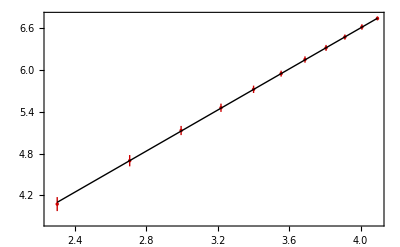

```mathematica
pltGRatScale=Show[{ListPlot[gLstRatLevDataLogAround,PlotStyle->darkRed,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotLegends->Placed[LineLegend[dataLab],{{legX,0.72},Right}]],Plot[fitLevRat["Function"][n],{n,Log[nLst⟦1⟧],Log[nLst⟦-1⟧]},PlotStyle->{Black,dataThick},PlotLegends->Placed[LineLegend[{logFitLab}],{{legX-0.04,0.85},Right}]],Graphics[Text[capTex⟦2⟧,Scaled[capLoc]]]},ImageSize->{Automatic,figW},Frame->True,BaseStyle->texStyle,FrameLabel->xyLabs]
```

```mathematica
Export["figs/gRatio0.4_log_fit_bar_capB.pdf",pltGRatScale];
```

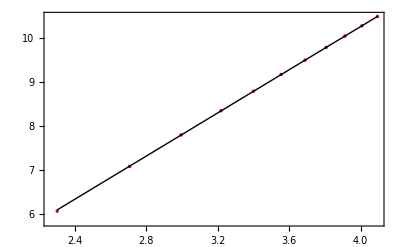

```mathematica
pltGTotalScale=Show[{ListPlot[gLstTotalDataLog,PlotStyle->darkRed,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotLegends->Placed[LineLegend[dataLab],{{legX,0.72},Right}]],Plot[fitTotal["Function"][n],{n,Log[nLst⟦1⟧],Log[nLst⟦-1⟧]},PlotStyle->{Black,dataThick},PlotLegends->Placed[LineLegend[{logFitLabTotal}],{{legX-0.04,0.85},Right}]],Graphics[Text[capTex⟦1⟧,Scaled[capLoc]]]},ImageSize->{Automatic,figW},Frame->True,BaseStyle->texStyle,FrameLabel->xyLabsTotal]
```

```mathematica
Export["figs/gTotal_log_fit_capA.pdf",pltGTotalScale];
```

```mathematica
LinearModelFit[Log[{nLst,gLstTotalMean}ᵀ],{n},{n}]
```

FittedModel[0.372002+2.47466 n]

```mathematica
Exp[0.3720017578386305]
```

1.45064

## Plot plateau scaling

### Temporary arrays

```mathematica
cMaxLst=ConstantArray[0,{nLen}];
cMaxVarLst=ConstantArray[0,{nLen}];
```

```mathematica
cMaxRatLst=ConstantArray[0,{nLen}];
cMaxVarRatLst=ConstantArray[0,{nLen}];
```

```mathematica
delCLst⟦4⟧//Dimensions
```

{24,126}

```mathematica
For[nId=1,nId<=nLen,nId++,
mSz=nLst⟦nId⟧;
res=Floor[√(mSz/nBase)80];
k3Low=Floor[k3LowRat res];
k3High=Floor[k3HighRat res];
cMaxLst⟦nId⟧=Mean/@delCLst⟦nId,All,k3Low;;k3High⟧;
cMaxVarLst⟦nId⟧=√(Total/@(delCVarLst⟦nId,All,k3Low;;k3High⟧^2))/(k3High-k3Low+1);
cMaxRatLst⟦nId⟧=cMaxLst⟦nId,levLowLst⟦nId⟧⟧;
cMaxVarRatLst⟦nId⟧=cMaxVarLst⟦nId,levLowLst⟦nId⟧⟧;
]
```

```mathematica
cMaxRatLst
```

{5.10333,5.08821,7.96362,9.96038,11.3841,13.7718,15.6749,18.872,19.4768,23.7341,22.5862}

```mathematica
xyLabsC=MaTeX[#,Magnification->labMag]&/@{"M","\\log \\langle \\left( \\Delta S_n \\right)^2 \\rangle_{\\rm sat}"};
```

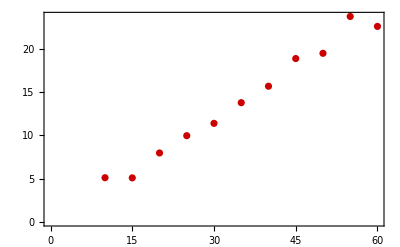

```mathematica
Show[ListPlot[{nLst,cMaxRatLst}ᵀ,PlotStyle->darkRed],ImageSize->{Automatic,figW},BaseStyle->texStyle,Frame->True,FrameLabel->xyLabsC]
```

```mathematica
cMaxVarRatLst
```

{1.28229,1.19227,1.66433,1.91417,2.27172,2.49504,2.72906,2.87207,3.35893,4.07268,3.48891}

```mathematica
cMaxVarLst⟦1⟧
```

{0.474769,0.766209,1.1223,1.28229,1.47862,1.20622,0.887929,0.686973,0.500031}

### Loading files

```mathematica
For[nId=1,nId<=nLen,nId++,
mSz=nLst⟦nId⟧;
divLst=Floor[√(mSz/nBase)divLstBase];
{attrLst,}]
```

## Misc

```mathematica
ExternalEvaluate[sessJul,"sqrt(36)"]
```

ExternalEvaluate::unknownSys: sessJul is not a known system in the ExternalEvaluate Framework.

ExternalEvaluate[sessJul,sqrt(36)]

```mathematica
readJulia["fileNotExist.jld2"]
```

Failure[…]

```mathematica
lst={{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

```mathematica
Map[f,lst,{2}]
```

{{f[1],f[2],f[3]},{f[4],f[5],f[6]}}